## Governing ODE and BCs for static landslide on non-planar base

The above ODE describes static equilibrium for a landslide with frictional boundary conditions

```mathematica
θv = π/6;
fv =1.1*Tan[θv]*(-x*0+1);
bmax = 0.05;
bv = bmax*Sin[ 1.5π x];
(*bv =4 bmax*(x^2+x);(* quadratic basal topography*)*)
eqnODE = -D[H[x],x] - 0.5*Tan[θv]*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*H[x] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv])
solss = NDSolve[{eqnODE,H[-0]==0.0},H,{x,-1,0}];
(*h = bv+ H[x]/. solss;*)
```

(0.320525 H[x] Sin[4.71239 x])/(1+0.136035 Cos[4.71239 x])-H'[x]==0.635085-(1/(√3)-0.235619 Cos[4.71239 x])/(1+0.136035 Cos[4.71239 x])+0.235619 Cos[4.71239 x]

## Instead of simply integrating , let us log-transform to such that the solution is strictly positive

```mathematica
eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*Tan[θv]*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*Exp[ϕ[x]] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv]);
sollogss = NDSolve[{eqnlogODE,ϕ[0]==-100},ϕ,{x,-1,0}];
H2 =  Exp[ϕ[x]/.sollogss];
h = bv+ H2;
```

NDSolve::ndsz: At x == -0.741125, step size is effectively zero; singularity or stiff system suspected.

## Plot results

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.979571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.959163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

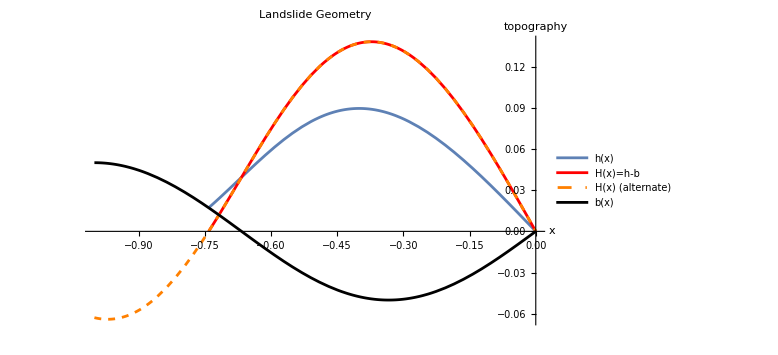

```mathematica
p1=Plot[{h,H2,H[x]/. solss,bv},{x,-1,0},PlotStyle->{DarkBlue,{Red,Thick},{Orange,Dashed},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","H(x) (alternate)","b(x)"},ImageSize->Large,PlotRange->Full]
```